```mathematica
DSolve[{-y''[x]+x*y'[x]+y[x]^2-y[x]==0,y'[0]==0, y[0]==a},y[x],x]
```

DSolve[{-y[x]+y[x]^2+x y'[x]-y''[x]==0,y'[0]==0,y[0]==a},y[x],x]

```mathematica
L[v_]:=D[v,t]-D[v,{x,2}]+D[v,x]*v^p
```

```mathematica
v[t_, x_]=t^(-1/4)*f[x/Sqrt[t]]
```

f[x/(√t)]/t^(1/4)

```mathematica
v[t_,x_]=λ*u[λ^2*t, λ*x]
```

λ u[t λ^2,x λ]

```mathematica
FullSimplify[L[v[t,x]],Assumptions->{t>0, λ>0}]
```

λ^2 ((λ u[t λ^2,x λ])^p u^(0,1)[t λ^2,x λ]+λ (-u^(0,2)[t λ^2,x λ]+u^(1,0)[t λ^2,x λ]))

```mathematica
FullSimplify[-FullSimplify[L[v[t,x]],Assumptions->{t>0}].10/.{x->y*Sqrt[t]}]
```

(.10 (f[y]+2 y f'[y]-4 f[y]^2 f'[y]+4 f''[y]))/(4 t^(5/4))

```mathematica
L[u_]:=1/4*u+u^2*Abs[D[u,x]]+x/2*D[u,x]+D[u,{x,2}]
```

```mathematica
L[u[-x]]/.{x->-y}
```

u[y]/4+Abs[u'[y]] u[y]^2+1/2 y u'[y]+u''[y]

```mathematica
L[u_]:=D[u,{x,2}]+x/2*D[u,x]+u/4-u^2*D[u,x]
```

```mathematica
FullSimplify[-L[u[x]*Exp[x^2/8]]/Exp[x^2/8]]
```

1/16 (-8 u[x]-3 x^2 u[x]-16 x u'[x]+4 ⅇ^(x^2/4) u[x]^2 (x u[x]+4 u'[x])-16 u''[x])

```mathematica
Collect[%,Derivative[_][u][_],Together]
```

1/16 u[x] (-8-3 x^2+4 ⅇ^(x^2/4) x u[x]^2)+(-x+ⅇ^(x^2/4) u[x]^2) u'[x]-u''[x]

1.50851

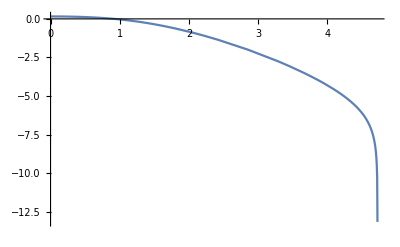

```mathematica
ysol=NDSolveValue[{y[x]/4-y[x]^2*y'[x]+x/2*y'[x]+y''[x]==0,y[0]==1.17, y'[0]==0.0},y,{x,0,20}];
NIntegrate[ysol[x]*Exp[-x^2/4],{x, 0,5}] 
Plot[Log[ysol[x]],{x,0,20},PlotRange->All]
```

```mathematica
ysol=NDSolveValue[{y[x]/4-y[x]^2*y'[x]+x/2*y'[x]+y''[x]==0,y[0]==1.17, y'[0]==0.0},y,{x,0,20}];
NIntegrate[ysol[x]*Exp[-x^2/4],{x, 0,5}] 
Plot[ysol[x],{x,0,20},PlotRange->All]
```

```mathematica
ψ[m_, r_]=LaguerreL[m, -1/2, r^2/4]*Exp[-r^2/4]
```

ⅇ^(-r^2/4) LaguerreL[m,-1/2,r^2/4]

```mathematica
D[ψ[m, r],r]+r/2*ψ[m, r]
```

-1/2 ⅇ^(-r^2/4) r LaguerreL[-1+m,1/2,r^2/4]

```mathematica
FullSimplify[D[ψ[m,r],r]+r*ψ[m,r]/2]
```

-1/2 ⅇ^(-r^2/4) r LaguerreL[-1+m,1/2,r^2/4]

```mathematica
%/.{r->2*Sqrt[z]}
```

-ⅇ^-z √z LaguerreL[-1+m,1/2,z]-ⅇ^-z √z LaguerreL[m,-1/2,z]

```mathematica
D[Exp[-r^2/4],r]/.{r->2*Sqrt[z]}
```

-ⅇ^-z √z

```mathematica
f[ r_]=LaguerreL[2, -1/2, r^2/4]*Exp[-r^2/4]/Sqrt[Integrate[LaguerreL[2, -1/2, z]^2/Sqrt[z]Exp[-z],{z, 0, ∞}]]
```

(ⅇ^(-r^2/4) (12-12 r^2+r^4))/(8 √6 π^(1/4))

```mathematica
Integrate[f[r]^2*Exp[r^2/4],{r, 0 , ∞}]
```

1

```mathematica
Cancel[(√2 ⅇ^(-r^2/4) (1/2-r^2/4))/π^(1/4)]
```

-(ⅇ^(-r^2/4) (-2+r^2))/(2 √2 π^(1/4))

```mathematica
Integrate[f[r]^6*Exp[r^2/4],{r, 0, ∞}]
```

223/(3125 √5 π)

```mathematica
N[%]
```

0.0101583

```mathematica
f[r]^4*D[f[r],r]^2
```

(ⅇ^(-r^2) (12-12 r^2+r^4)^4 ((ⅇ^(-r^2/4) (-24 r+4 r^3))/(8 √6 π^(1/4))-(ⅇ^(-r^2/4) r (12-12 r^2+r^4))/(16 √6 π^(1/4)))^2)/(147456 π)

```mathematica
Integrate[%*Exp[r^2/4],{r, 0, ∞}]
```

268011/(19531250 √5 π)

```mathematica
N[%]
```

0.00195338

```mathematica
FullSimplify[D[u[x]^2*ψ[m,x]*Exp[x^2/4],x]*Exp[-x^2/4]]
```

u[x] (2 ψ[m,x] u'[x]+u[x] (1/2 x ψ[m,x]+ψ^(0,1)[m,x]))

```mathematica
FullSimplify[Gamma[m+1/2]/(m+1/2)]
```

Gamma[1/2+m]/(1/2+m)

```mathematica
(FullSimplify[Sum[1/(m+1/2)Gamma[m+1/2]/Factorial[m],{m,n,∞}]]/.{n->501})/Pi
```

(496357522430106709531544096218594521933427557486121204822708017754439749424363985434482315531486425192864214018849374139417877406585231370838184135257459334821330041659356810440733655013167828372132460694934794202359281493524062478710071759447366625424303548160553891234235412515788648382763188765 HypergeometricPFQ[{1,1003/2,1003/2},{502,1005/2},1])/(9877969972498401864993293421021891691112950607910387943622073892789173752558004879234172554707196192113763390958693072294693995602476020089423282451675248647377179667416087939685053151541873396418739011672339719125489602105883238843605735825289792374370321752867281060811958751054763106615548975251456 √π)

```mathematica
N[%]
```

0.0284444

```mathematica
Sqrt[%]
```

0.168655

```mathematica
%*1.17^2*2.95
```

0.681071

```mathematica
Integrate[Exp[-r^2/4]]
```

```mathematica
u[r_] = (1+Abs[r])*Exp[-r^2/4]
```

ⅇ^(-r^2/4) (1+Abs[r])

```mathematica
v[r_] = (2+4*Abs[r]^3)*Exp[-r^2/4]
```

ⅇ^(-r^2/4) (2+4 r^3)

```mathematica
D[Exp[r^2/4]*D[u[r],r]]*v[r]
```

(2+r^2+r^3) (ⅇ^(-r^2/4)-1/2 ⅇ^(-r^2/4) r (1+r))

```mathematica
Integrate[%,{r, 0, ∞}]
```

-10 (3+√π)

```mathematica
FullSimplify[D[Exp[r^2/4]*D[v[r],r],r]*u[r]-D[Exp[r^2/4]*D[u[r],r],r]*v[r]]
```

ⅇ^(-r^2/4) (-6 r (-4+r^2) (1+Abs[r])+(r+2 r^4) Abs'[r]-2 (1+2 r^3) Abs''[r])

```mathematica
Integrate[%,{r, 0, ∞}]
```

$Aborted

```mathematica
Integrate[u[r]*D[Exp[r^2/4]*D[v[r],r],r],{r, 0, ∞}]
```

-14 (1+√π)

```mathematica
Integrate[v[r]*D[Exp[r^2/4]*D[u[r],r],r],{r, 0, ∞}]
```

-2 (8+7 √π)

```mathematica
Integrate[v[r]*D[r*Exp[r^2/4]*D[v[r],r],r],{r, 0, ∞}]
```

-114-(9 √π)/4-7 √2 Gamma[1/4]

```mathematica
Integrate[D[u[r],r]^2*Exp[r^2/4],{r, 0, ∞}]
```

(7 Gamma[1/6])/(9 2^(2/3))

```mathematica
In[102]
```

ⅇ^(-r^2/4) (2+r^2+r^3)

```mathematica
Integrate[Exp[-3y^2/8],{y, x, ∞}]^2*Exp[x^2/4]
```

2/3 ⅇ^(x^2/4) π Erfc[1/2 √(3/2) x]^2

```mathematica
Integrate[Integrate[Exp[-y^2/8],{y, x, ∞}]^2*Exp[x^2/4], {x, 0, ∞}]
```

∫_0^∞ 2 ⅇ^(x^2/4) π Erfc[x/(2 √2)]^2ⅆx

```mathematica
Integrate[2*Erfc[x/(2*Sqrt[2])]^2Exp[x^2/4],{x ,0, ∞}]
```

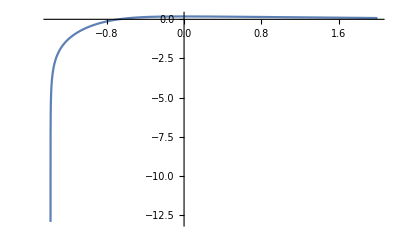

```mathematica
ysol=NDSolveValue[{y[x]/4+3*y[x]^2*y'[x]+x/2*y'[x]+y''[x]==0,y[0]==1.2, y'[0]==0.0},y,{x,-2,2}];
Plot[Log[ysol[x]],{x,-2,2},PlotRange->All]
```

```mathematica
FullSimplify[Sum[1/(m+1/2)Gamma[m+1/2]/Factorial[m],{m,n,∞}]]
```

Gamma[1/2+n]^2 HypergeometricPFQRegularized[{1,1/2+n,1/2+n},{1+n,3/2+n},1]

```mathematica
Series[Gamma[1/2+n]^2 HypergeometricPFQRegularized[{1,1/2+n,1/2+n},{1+n,3/2+n},1], n ->∞]
```

ⅇ^(2 (-1+Log[n]) n+O[1/n]^2) HypergeometricPFQRegularized[{1,1/2+n,1/2+n},{1+n,3/2+n},1] (2 π+O[1/n]^1)

```mathematica
Sum[1/(m+1/2)Gamma[m+1/2]/Factorial[m],{m,0,∞}]
```

π^(3/2)

```mathematica
Integrate[Gamma[x+1/2]/(x+1/2)/Gamma[x+1],{x,y,∞}]
```

∫_y^∞ Gamma[1/2+x]/((1/2+x) Gamma[1+x])ⅆx

```mathematica
Table[Log[N[Gamma[1/2+n]^2 HypergeometricPFQRegularized[{1,1/2+n,1/2+n},{1+n,3/2+n},1] ]]/Log[n],{n, 1000, 10000,1000}]
```

{-0.399651,-0.408805,-0.413424,-0.416427,-0.418617,-0.420323,-0.42171,-0.422873,-0.423871,-0.424742}

```mathematica
1/0.36913680300785016663350801094649618683266140971179078401711808500414664985984462190042106047498154840199307747741982690299345726181540394467674023314104238347454203094912123583295240479630563969832687235004597619`200.2913253153564
```

2.7090227575567254396447008621186243836976453446959155610198811694992026725504008445811999879498516567448023072241935536037196959869144164819900814963784499304893047441779554216616538133932426550908889